# Check our Fortan implementation of EMT

## We are sure that our implementation is right. If you doubt us, screw u.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sjanke/git/mdhag/pes_fitting_programs/EMT_potential

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot};
```

```mathematica
pbc[r_,celldim_]:=r-celldim Round[r/celldim]
```

## Equilibrium configuration

#### Import Fit Data and define geometry

read in the positions of the lattice and h atoms

```mathematica
data=Import["ref_conf_Au111.dat"];data=Import["../Fit_with_static_lattice/derivatives/reindeer.dat"];
dataH=Import["hau111_plot.E.dat"];
rAu=data[[7;;]];
rHsrules=MapThread[#1->#2&,{{x,y,z},#}]&/@dataH[[All, 2;;4]];
```

configure positions of atoms for operation

```mathematica
nAu=Length[rAu]
nlayer=data[[2,1]]
nperl=nAu/nlayer
dnn=data[[3,1]]
celldim=data[[{4,5},1]]
```

144

4

36

2.97056

{17.8233,15.4355}

Gets the Geometries set. Again, we get ‘periodic boundary conditions’ by acting as if the atom in the middle of each layer is the same as each other atom of that layer.

```mathematica
(*rAul=Table[rAu[[45+90(i-1)]],{i,nlayer}];*)rAul=Table[rAu[[1+4(i-1)]],{i,nlayer}];
rrAuAu=Table[Select[Norm[#-rAul[[i]]]&/@rAu,#>0&],{i,nlayer}];
rrHAu=Table[√(({x,y,z}-rAu[[j]]).({x,y,z}-rAu[[j]])),{j,nAu}];
rpl=(rrHAu/.rHsrules)ᵀ;
```

#### Read in potential parameters (_not_ fitting parameters)

```mathematica
β=(16π/3)^(1/3)/(√2);
bohr=0.5291772082952705
```

0.529177

Fit paramters, fit 119

```mathematica
{η2H, κH, λH,eoH,soH, voH, noH}=Import["parameters_H_f119.nml", "Table"][[3;;-2,2]];
{η2Au, κAu, λAu,eoAu,soAu, voAu, noAu}=Import["parameters_Au_f119.nml", "Table"][[3;;-2,2]];
subruls={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

Fit paramters, Strömqvist

```mathematica
{η2H, noH,eoH,λH,voH,κH,soH}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.H.nml", "Table"][[3;;-2,2]]
{η2Au, noAu,eoAu,λAu, voAu, κAu,soAu}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.Au.nml", "Table"][[3;;-2,2]]
κAu=1
paars={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

{5.4254,0.182205,-2.371,7.72709,0.427,8.86282,0.680411}

{3.1634,0.0474408,-3.8,4.12338,2.321,5.42918,1.64174}

1

#### Derivatives for χ

In our Fortran program, they form an array in which the first element corresponds to the derivative with respect to nop and the second to the derivative with respect to nol

```mathematica
χlp = nop/nol;
D[χlp,#]&/@{nop,nol}
{χlp,%}/.paars
```

{1/nol,-nop/nol^2}

{3.84068,{21.0789,-80.9573}}

```mathematica
χpl = nol/nop;
D[χpl,#]&/@{nop,nol}
{χpl,%}/.paars
```

{-nol/nop^2,1/nop}

{0.26037,{-1.429,5.48832}}

#### Gamma

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
Log[9999.]
```

9.21024

```mathematica
rc=5.14515;
rr= (4rc)/(√3+2);
acut=Log[9999]/(rr-rc);
rAunn=Table[soAu β √i,{i,3} ]
rHnn=Table[soH β √i,{i,3} ]
```

{2.97056,4.20101,5.14517}

{1.23114,1.74109,2.13239}

```mathematica
xAu1=1/(1+Exp[acut(rAunn[[1]]-rc)]);
xAu2=1/(2(1+Exp[acut(rAunn[[2]]-rc)]));
xAu3=2/(1+Exp[acut(rAunn[[3]]-rc)]);
xAu=List[xAu1,xAu2,xAu3];
xH1=1/(1+Exp[acut(rHnn[[1]]-rc)]);
xH2=1/(2(1+Exp[acut(rHnn[[2]]-rc)]));
xH3=2/(1+Exp[acut(rHnn[[3]]-rc)]);
xH=List[xH1,xH2,xH3];
```

```mathematica
N[Sqrt[0.5],10]
xAu
xH
```

0.707107

{1.,0.5,0.999778}

{1.,0.5,2.}

```mathematica
γ1l=Total[xAu Exp[-η2l(rAunn-β sol)]];
γ2l=Total[xAu Exp[-κl/β(rAunn-β sol)]];
γ1p=Total[xH Exp[-η2p(rHnn-β sop)]];
γ2p=Total[xH Exp[-κp/β(rHnn-β sop)]];
```

```mathematica
{γ1l,γ2l,γ1p,γ2p}^(-1) /.paars
```

{0.988898,0.643552,0.955582,0.938675}

```mathematica
{D[γ1l,η2l],D[γ1l,sol],D[γ2l,κl],D[γ2l,sol],D[γ1p,η2p],D[γ1p,sop],D[γ2p,κp],D[γ2p,sop]}/.paars
```

{-0.0147856,5.78812,-0.533494,1.55388,-0.0295922,10.273,-0.0236462,9.44184}

#### Theta. Part of the cut-off, has also no derivative.

```mathematica
xσAuAu=Table[Exp[acut(rrAuAu[[i]]-rc)],{i,nlayer}];
xσHAu=Exp[acut(rpl-rc)];
θAuAu=Table[1/(1+xσAuAu[[i]]),{i,nlayer}];
θHAu=1/(1+xσHAu);
```

#### Derivatives of σ

```mathematica
σll=Table[Total[Exp[-η2l (rrAuAu[[i]]-β sol)] θAuAu[[i]]/γ1l],{i,nlayer}];
σlp=Exp[-η2p(rpl-β sop)] θHAu/γ1l;
σpl=Total[Exp[-η2l(rpl-β sol)] θHAu/γ1p];
```

```mathematica
σll/.paars
```

{8.85746,12.2172,12.3363,8.97663}

```mathematica
{D[σlp[[9,1]],η2l],D[σpl[[1]],η2l]}/.paars//Chop
{D[σlp[[9,1]],η2p],D[σpl[[1]],η2p]}/.paars//Chop
{D[σlp[[9,1]],sol],D[σpl[[1]],sol]}/.paars//Chop
{D[σlp[[9,1]],sop],D[σpl[[1]],sop]}/.paars//Chop
```

{0.0022869,330.779}

{-0.261678,100.691}

{-3.93529,2005.59}

{1.2283,-625.993}

```mathematica
{D[σll,η2l],D[σll,sol]}/.paars
```

{{-0.0191537,0.0584712,0.086716,0.00891267},{2.84217×10^-14,4.26326×10^-14,4.26326×10^-14,2.84217×10^-14}}

#### Derivatives of ds

```mathematica
(*dsl=-1/(β η2l)Table[Log[(σll[[Ceiling[i/90]]]+χlp σlp[[i]])/12],{i,nAu}]*)dsl=-1/(β η2l)Table[Log[(σll[[1+Quotient[Mod[i,16,1]-1,4]]]+χlp σlp[[i]])/12],{i,nAu}];
```

```mathematica
dsp=-Log[(χpl σpl)/12]/(β η2p);
```

```mathematica
(*dslref=-1/(β η2l)Table[Log[σll[[Ceiling[i/90]]]/12],{i,nAu}];*)
dslref=-1/(β η2l)Table[Log[σll[[1+Quotient[Mod[i,16,1]-1,4]]]/12],{i,nAu}];
```

```mathematica
dslref/.paars
```

{0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684,0.0528993,0.0528993,0.0528993,0.0528993,-0.00237304,-0.00237304,-0.00237304,-0.00237304,-0.00370085,-0.00370085,-0.00370085,-0.00370085,0.0510684,0.0510684,0.0510684,0.0510684}

```mathematica
dsp[[55]]/.paars
```

2.96981

```mathematica
{D[dslref[[1]],η2l],D[dslref[[1]],nol],D[dslref[[1]],sol]}/.paars
```

{-0.0168794,0,2.80059×10^-16}

```mathematica
{D[dsl[[1,55]],η2l],D[dsl[[1,55]],nol],D[dsl[[1,55]],sol]}/.paars
```

{-0.0168794,2.19785×10^-18,1.40029×10^-16}

```mathematica
{D[dsl[[1,26]],η2p],D[dsl[[1,26]],nop],D[dsl[[1,26]],sop]}/.paars
```

{-0.21446,-0.956047,-1.71004}

```mathematica
{D[dsp[[55]],η2l],D[dsp[[55]],nol],D[dsp[[55]],sol]}/.paars
{D[dsp[[55]],η2p],D[dsp[[55]],nop],D[dsp[[55]],sop]}/.paars
```

{0.288226,-2.14725,-0.583072}

{-0.55027,0.559079,1.}

#### Derivatives of Pair Potentials

```mathematica
vll=-vol/2 nperl Total[  Exp[-κl(Flatten[rrAuAu]/β- sol)] Flatten[θAuAu]/γ2l];
vlp=-vol/2 χlp Total[Exp[-κp (rpl/β- sop)] θHAu/γ2l];
vpl=-vop/2 χpl Total[Exp[-κl (rpl/β- sol)] θHAu/γ2p];
```

```mathematica
vll/.paars
{D[vll,κl],D[vll,sol],D[vll,vol]}/.paars
```

-1763.58

{-4.6814,0.,-759.835}

```mathematica
{vlp[[1]],vpl[[1]]}/.paars
```

{-1.21413,-7.2372}

```mathematica
{D[vlp[[1]],nol],D[vlp[[1]],nop]}/.paars
{D[vpl[[1]],nol],D[vpl[[1]],nop]}/.paars
```

{25.5924,-6.66351}

{-152.552,39.7201}

```mathematica
{D[vlp[[1]],vol],D[vlp[[1]],vop]}/.paars
{D[vpl[[1]],vol],D[vpl[[1]],vop]}/.paars
```

{-0.523105,0}

{0,-16.949}

```mathematica
{D[vlp[[1]],κl],D[vlp[[1]],κp]}/.paars
{D[vpl[[1]],κl],D[vpl[[1]],κp]}/.paars
```

{-0.0122567,0.340302}

{-4.69253,-0.160638}

```mathematica
{D[vlp[[1]],sol],D[vlp[[1]],sop]}/.paars
{D[vpl[[1]],sol],D[vpl[[1]],sop]}/.paars
```

{6.59171,-10.7606}

{-39.2921,64.142}

#### Derivatives of Reference Pair Potentials

```mathematica
vrefl= 6vol Total[Exp[-κl dsl]];
```

```mathematica
vreflref= 6vol Total[Exp[-κl dslref]];
```

```mathematica
vrefp=6vop Exp[-κp dsp];
```

```mathematica
vreflref/.paars
```

1775.47

```mathematica
{vrefl[[1]],vrefp[[1]]}/.paars
```

{1776.36,7.9077}

```mathematica
{D[vrefl[[1]],η2l],D[vrefl[[1]],nol],D[vrefl[[1]],vol],D[vrefl[[1]],κl],D[vrefl[[1]],sol]}/.paars
```

{69.2131,-18.6171,765.341,-36.0379,-5.05537}

```mathematica
{D[vrefl[[1]],η2p],D[vrefl[[1]],nop],D[vrefl[[1]],vop],D[vrefl[[1]],κp],D[vrefl[[1]],sop]}/.paars
```

{-0.444281,4.84735,0,0,8.67023}

```mathematica
{D[vreflref,η2l],D[vreflref,nol],D[vreflref,vol],D[vreflref,κl],D[vreflref,sol]}/.paars
```

{69.4867,0,764.96,-36.2047,-2.83167×10^-12}

```mathematica
{D[vrefp[[1]],η2l],D[vrefp[[1]],nol],D[vrefp[[1]],sol]}/.paars
```

{8.45957,150.489,40.8643}

```mathematica
{D[vrefp[[1]],η2p],D[vrefp[[1]],nop],D[vrefp[[1]],vop],D[vrefp[[1]],κp],D[vrefp[[1]],sop]}/.paars
```

{-1.44083,-39.1828,18.5192,1.00559,-70.0845}

#### Derivatives of Ecoh

```mathematica
ecohl=Total[eol((1+λl dsl)Exp[-λl dsl]-1)];
ecohp=eop((1+λp dsp)Exp[-λp dsp]- 1 0);
```

```mathematica
ecohlref=Total[eol((1+λl dslref)Exp[-λl dslref]-1)];
```

```mathematica
ecohlref/.paars
```

5.47935

```mathematica
{D[ecohlref,η2l],D[ecohlref,nol],D[ecohlref,eol],D[ecohlref,λl],D[ecohlref,vol],D[ecohlref,κl],D[ecohlref,sol]}/.paars
```

{-3.2888,0,-1.44193,2.47196,0,0,5.03277×10^-14}

```mathematica
ecoh=ecohl[[55]]+ecohp[[55]];
```

```mathematica
ecohl[[55]]/.paars
```

5.47935

```mathematica
{D[ecoh,η2l],D[ecoh,nol],D[ecoh,eol],D[ecoh,λl],D[ecoh,vol],D[ecoh,κl],D[ecoh,sol]}/.paars
```

{-3.2888,-9.75883×10^-8,-1.44193,2.47196,0,0,-2.64995×10^-8}

```mathematica
{D[ecoh,η2p],D[ecoh,nop],D[ecoh,eop],D[ecoh,λp],D[ecoh,vop],D[ecoh,κp],D[ecoh,sop]}/.paars
```

{-2.50087×10^-8,2.54091×10^-8,2.58877×10^-9,1.74674×10^-8,0,0,4.54481×10^-8}

#### Final Derivatives

```mathematica
eemm=ecohl+ecohp+vll+vlp+vpl+ 6vol Total[Exp[-κl dsl]]+ 6vop Exp[-κp dsp];
```

```mathematica
eemmref=ecohlref+vll+vreflref;
eemmref/.paars
```

275.6

```mathematica
{D[eemmref,η2l],D[eemmref,nol],D[eemmref,eol],D[eemmref,λl],D[eemmref,vol],D[eemmref,κl],D[eemmref,sol]}/.paars
```

{66.1979,0,-1.44193,2.47196,5.12564,-40.8861,-2.78134×10^-12}

```mathematica
eemm[[1]]/. paars
```

17.6093

```mathematica
{D[eemm[[1]],η2l],D[eemm[[1]],nol],D[eemm[[1]],eol],D[eemm[[1]],λl],D[eemm[[1]],vol],D[eemm[[1]],κl],D[eemm[[1]],sol]}/. paars
```

{80.1877,108.08,-1.44281,2.47364,4.98327,-45.4241,31.1235}

```mathematica
{D[eemm[[1]],η2p],D[eemm[[1]],nop],D[eemm[[1]],eop],D[eemm[[1]],λp],D[eemm[[1]],vop],D[eemm[[1]],κp],D[eemm[[1]],sop]}/. paars
```

{-2.87573,-28.141,0.0464225,0.791474,1.57025,1.18525,-56.0799}

Strömqvist

```mathematica
{D[eemmref,η2l],D[eemmref,nol],D[eemmref,eol],D[eemmref,λl],D[eemmref,vol],D[eemmref,κl],D[eemmref,sol]}/.paars
```

{166.774,0,-3.44773,5.91821,12.9103,-103.048,-6.26758×10^-12}

```mathematica
{D[eemm[[1]],η2l],D[eemm[[1]],nol],D[eemm[[1]],eol],D[eemm[[1]],λl],D[eemm[[1]],vol],D[eemm[[1]],κl],D[eemm[[1]],sol]}/. paars
```

{180.829,108.436,-3.44811,5.91892,12.7678,-107.604,31.2199}

```mathematica
{D[eemm[[1]],η2p],D[eemm[[1]],nop],D[eemm[[1]],eop],D[eemm[[1]],λp],D[eemm[[1]],vop],D[eemm[[1]],κp],D[eemm[[1]],sop]}/. paars
```

{-2.88483,-28.2334,0.0431287,0.79449,1.57829,1.18827,-56.2452}

#### Reference energy

```mathematica
eemm0check=eemm-eemmref;
```

```mathematica
{D[eemm0check[[1]],η2p],D[eemm0check[[1]],nop],D[eemm0check[[1]],eop],D[eemm0check[[1]],λp],D[eemm0check[[1]],vop],D[eemm0check[[1]],κp],D[eemm0check[[1]],sop]}/. subruls
```

```mathematica
{-34.199497895566154,-1.4306274801689753,0.9983766983829074,0.004436343593595016,1.3264926855519565,18.056882681393613,-5.113597458586161}
```

```mathematica
{D[eemm0check[[1]],η2l],D[eemm0check[[1]],nol],D[eemm0check[[1]],eol],D[eemm0check[[1]],λl],D[eemm0check[[1]],vol],D[eemm0check[[1]],κl],D[eemm0check[[1]],sol]}/. subruls
```

{-5.97126,24.4075,-0.177676,0.359016,-0.0520612,4.18576,-9.15915}

strömqvist

```mathematica
{D[eemm0check[[1]],η2p],D[eemm0check[[1]],nop],D[eemm0check[[1]],eop],D[eemm0check[[1]],λp],D[eemm0check[[1]],vop],D[eemm0check[[1]],κp],D[eemm0check[[1]],sop]}/. paars
```

{-2.88483,-28.2334,0.0431287,0.79449,1.57829,1.18827,-56.2452}

```mathematica
{D[eemm0check[[1]],η2l],D[eemm0check[[1]],nol],D[eemm0check[[1]],eol],D[eemm0check[[1]],λl],D[eemm0check[[1]],vol],D[eemm0check[[1]],κl],D[eemm0check[[1]],sol]}/. paars
```

{14.0557,108.436,-0.000378037,0.000700446,-0.142487,-4.5563,31.2199}

## AIMD configuration

### Energy

#### Import Fit Data and define geometry

read in the positions of the lattice and h atoms

```mathematica
data=Import["../Fit_with_static_lattice/derivatives/aimdreindeer.dat"];
dataH=data[[8]]
rAu=data[[9;;]];
rHsrules=MapThread[#1->#2&,{{x,y,z},#}]&/@{dataH};
```

{0.55132,4.32308,1.89133}

configure positions of atoms for operation

```mathematica
nAu=Length[rAu]
nlayer=data[[2,1]]
nperl=nAu/nlayer
dnn=data[[3,1]]
celldim=data[[{4,5,6},1]]
```

144

4

36

2.97056

{17.8233,15.4355,20.2573}

Gets the Geometries set. Again, we get ‘periodic boundary conditions’ by acting as if the atom in the middle of each layer is the same as each other atom of that layer.

```mathematica
rrAuAu=Table[Norm[pbc[rAu[[i]]-rAu[[j]],celldim]],{i, nAu},{j,nAu}];
rpl=Table[Norm[pbc[dataH-rAu[[i]],celldim]],{i, nAu}];
```

#### Read in potential parameters (_not_ fitting parameters)

```mathematica
β=(16π/3)^(1/3)/(√2);
bohr=0.5291772082952705
```

0.529177

Fit paramters, fit 119

```mathematica
{η2H, κH, λH,eoH,soH, voH, noH}=Import["parameters_H_f119.nml", "Table"][[3;;-2,2]];
{η2Au, κAu, λAu,eoAu,soAu, voAu, noAu}=Import["parameters_Au_f119.nml", "Table"][[3;;-2,2]];
subruls={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

Fit paramters, Strömqvist

```mathematica
{η2H, noH,eoH,λH,voH,κH,soH}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.H.nml", "Table"][[3;;-2,2]]
{η2Au, noAu,eoAu,λAu, voAu, κAu,soAu}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.Au.nml", "Table"][[3;;-2,2]]
paars={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

{5.4254,0.182205,-2.371,7.72709,0.427,8.86282,0.680411}

{3.1634,0.0474408,-3.8,4.12338,2.321,5.42918,1.64174}

#### χ

In our Fortran program, they form an array in which the first element corresponds to the derivative with respect to nop and the second to the derivative with respect to nol

```mathematica
χlp = nop/nol;
χpl = nol/nop;
```

```mathematica
{χlp,χpl}/.paars
```

{3.84068,0.26037}

#### γ

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
Log[9999.]
```

9.21024

```mathematica
rc=5.14515;
rr= (4rc)/(√3+2);
acut=Log[9999]/(rr-rc);
rAunn=Table[soAu β √i,{i,3} ]
rHnn=Table[soH β √i,{i,3} ]
```

{2.97056,4.20101,5.14517}

{1.23114,1.74109,2.13239}

```mathematica
xAu1=1/(1+Exp[acut(rAunn[[1]]-rc)]);
xAu2=1/(2(1+Exp[acut(rAunn[[2]]-rc)]));
xAu3=2/(1+Exp[acut(rAunn[[3]]-rc)]);
xAu=List[xAu1,xAu2,xAu3];
xH1=1/(1+Exp[acut(rHnn[[1]]-rc)]);
xH2=1/(2(1+Exp[acut(rHnn[[2]]-rc)]));
xH3=2/(1+Exp[acut(rHnn[[3]]-rc)]);
xH=List[xH1,xH2,xH3];
```

```mathematica
N[Sqrt[0.5],10]
xAu
xH
```

0.707107

{1.,0.5,0.999778}

{1.,0.5,2.}

```mathematica
γ1l=Total[xAu Exp[-η2l(rAunn-β sol)]];
γ2l=Total[xAu Exp[-κl/β(rAunn-β sol)]];
γ1p=Total[xH Exp[-η2p(rHnn-β sop)]];
γ2p=Total[xH Exp[-κp/β(rHnn-β sop)]];
```

```mathematica
{γ1l,γ2l,γ1p,γ2p}^(-1) /.paars
```

{0.988898,0.986264,0.955582,0.938675}

#### θ

```mathematica
xσAuAu=Exp[acut(rrAuAu-rc)];
xσHAu=Exp[acut(rpl-rc)];
θAuAu=1/(1+xσAuAu)-IdentityMatrix[nAu];
θHAu=1/(1+xσHAu);
```

Thread::tdlen: Objects of unequal length in {{1., 1., 1., 1., 0.46161, 1., 0.460581, 0.613075, 3.57037×10^-9, « 34 », 1.40684×10^-46, 6.19879×10^-30, 7.43663×10^-61, 2.37809×10^-41, 2.40579×10^-9, 0.5, 1.64358×10^-41, « 93 »}, « 2 », {« 1 »}} + « 1 » cannot be combined.

#### σ

```mathematica
σll=Table[Sum[Exp[-η2l (rrAuAu[[i,j]]-β sol)] θAuAu[[i,j]]/γ1l,{j,1,nAu}],{i,nAu}];
σlp=Exp[-η2p(rpl-β sop)] θHAu/γ1l;
σpl=Total[Exp[-η2l(rpl-β sol)] θHAu/γ1p];
```

Part::partw: Part 5 of « 1 » does not exist.

Thread::tdlen: Objects of unequal length in {{1., 1., 1., 1., 0.46161, 1., 0.460581, 0.613075, 3.57037×10^-9, « 34 », 1.40684×10^-46, 6.19879×10^-30, 7.43663×10^-61, 2.37809×10^-41, 2.40579×10^-9, 0.5, 1.64358×10^-41, « 93 »}, « 2 », {« 1 »}} + « 1 » cannot be combined.

Part::partw: Part 5 of « 1 » does not exist.

Part::partw: Part 6 of « 1 » does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {{1., 1., 1., 1., 0.46161, 1., 0.460581, 0.613075, 3.57037×10^-9, « 34 », 1.40684×10^-46, 6.19879×10^-30, 7.43663×10^-61, 2.37809×10^-41, 2.40579×10^-9, 0.5, 1.64358×10^-41, « 93 »}, « 2 », {« 1 »}} + « 1 » cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

#### ds

```mathematica
dsl=-1/(β η2l)Log[(σll+χlp σlp)/12];
dsp=-Log[(χpl σpl)/12]/(β η2p);
```

Thread::tdlen: Objects of unequal length in {1.61308\ ⅇ^-(2.97056  + Times[« 4 »])\ η2l/1.\ Power[« 2 »] + 0.5\ Power[« 2 »] + 0.999778\ Power[« 2 »] + « 49 » + « 93 », 1.\ ⅇ^-(« 18 »  + « 1 »)\ η2l/1.\ Power[« 2 »] + « 19 »\ Power[« 1 »] + 0.999778\ Power[« 2 »] + 1.\ ⅇ^« 1 »/« 1 » + « 47 » + « 1 »\ « 1 »/« 1 » + « 93 », « 47 », « 1 », « 93 »} + « 1 » cannot be combined.

Thread::tdlen: Objects of unequal length in {-ⅇ^-(2.98152  - Power[« 2 »]\ Power[« 2 »]\ sol)\ η2l/1.\ ⅇ^Times[« 3 »] + 0.5\ ⅇ^Times[« 3 »] + 0.999778\ ⅇ^Times[« 3 »], « 49 », « 94 »} + {5.46367×10^-8\ ⅇ^-(« 18 »  - « 1 »)\ η2p\ nop/(1.\ ⅇ^Times[« 3 »] + « 19 »\ ⅇ^« 1 » + 0.999778\ ⅇ^Times « 1 » « 1 »])\ nol, « 1 »/(« 1 »)\ « 3 », « 47 », « 1 »/« 1 », « 510 »} cannot be combined.

$Aborted

```mathematica
dsp/.paars
```

-0.0504781

#### Pair-wise Correction

```mathematica
vll=-vol/2 Total[  Exp[-κl(Flatten[rrAuAu]/β- sol)] Flatten[θAuAu]/γ2l];vlp=-vol/2 χlp Total[Exp[-κp (rpl/β- sop)] θHAu/γ2l];
vpl=-vop/2 χpl Total[Exp[-κl (rpl/β- sol)] θHAu/γ2p];
```

```mathematica
vll/.paars
vlp/.paars
vpl/.paars
```

-1747.81

-0.0637859

-0.863607

#### Reference Pair-wise Correction

```mathematica
vrefl= 6vol Total[Exp[-κl dsl]];
vrefp=6vop Exp[-κp dsp];
```

```mathematica
{vrefl,vrefp}/.paars
```

{1853.9,4.0075}

#### Ecoh

```mathematica
ecohl=Total[eol((1+λl dsl)Exp[-λl dsl]-1)];
ecohp=eop((1+λp dsp)Exp[-λp dsp]- 1 0);
```

```mathematica
{ecohl,ecohp}/.paars
```

{2.62571,-2.1361}

```mathematica
ecoh=ecohl+ecohp;
```

```mathematica
ecoh/.paars
```

0.489604

```mathematica
ecohl/.paars
```

2.62571

#### Great Final

```mathematica
eemm=ecohl+ecohp+vll+vlp+vpl+ 6vol Total[Exp[-κl dsl]]+ 6vop Exp[-κp dsp];
```

```mathematica
eemm/.paars
```

109.659

```mathematica
eemm0=eemm-eemmref
```

```mathematica
eemm0/.paars
```

### Derivatives

#### χ

```mathematica
D[χlp,#]&/@{nop,nol}
%/.paars
```

{1/nol,-nop/nol^2}

{21.0789,-80.9573}

```mathematica
D[χpl,#]&/@{nop,nol}
%/.paars
```

{-nol/nop^2,1/nop}

{-1.429,5.48832}

#### γ

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
{D[γ1l,η2l],D[γ1l,sol],D[γ2l,κl],D[γ2l,sol],D[γ1p,η2p],D[γ1p,sop],D[γ2p,κp],D[γ2p,sop]}/.paars
```

{-0.0147856,5.78812,-0.0102357,5.50479,-0.0295922,10.273,-0.0236462,9.44184}

#### σ

```mathematica
{D[σlp[[9]],η2l],D[σpl,η2l]}/.paars//Chop
{D[σlp[[9]],η2p],D[σpl,η2p]}/.paars//Chop
{D[σlp[[9]],sol],D[σpl,sol]}/.paars//Chop
{D[σlp[[9]],sop],D[σpl,sop]}/.paars//Chop
```

{0,12.8305}

{0,0.502257}

{0,101.665}

{0,-174.36}

```mathematica
{D[σll[[2]],η2l],D[σll[[2]],sol]}/.paars
```

{0.00588885,-1.42109×10^-14}

#### ds

```mathematica
{D[dsl[[1]],η2l],D[dsl[[1]],nol],D[dsl[[1]],sol]}/.paars
```

{-0.0175314,5.71551×10^-9,1.55201×10^-9}

```mathematica
{D[dsl[[1,26]],η2p],D[dsl[[1,26]],nop],D[dsl[[1,26]],sop]}/.paars
```

{-0.21446,-0.956047,-1.71004}

```mathematica
{D[dsp[[55]],η2l],D[dsp[[55]],nol],D[dsp[[55]],sol]}/.paars
{D[dsp[[55]],η2p],D[dsp[[55]],nop],D[dsp[[55]],sop]}/.paars
```

{0.288226,-2.14725,-0.583072}

{-0.55027,0.559079,1.}

#### Pair-wise Correction

```mathematica
{D[vll,κl],D[vll,sol],D[vll,vol]}/.paars
```

{-5.29299,0.,-753.041}

```mathematica
{D[vlp,nol],D[vlp,nop]}/.paars
{D[vpl,nol],D[vpl,nop]}/.paars
```

{1.34454,-0.350078}

{-18.2039,4.73975}

```mathematica
{D[vlp,vol],D[vlp,vop]}/.paars
{D[vpl,vol],D[vpl,vop]}/.paars
```

{-0.0274821,0}

{0,-2.0225}

```mathematica
{D[vlp,κl],D[vlp,κp]}/.paars
{D[vpl,κl],D[vpl,κp]}/.paars
```

{-0.000643927,0.0321631}

{-0.335232,-0.0191687}

```mathematica
{D[vlp,sol],D[vlp,sop]}/.paars
{D[vpl,sol],D[vpl,sop]}/.paars
```

{0.346305,-0.565323}

{-4.68868,7.65399}

#### Reference Pair-wise Correction

```mathematica
{D[vrefl,η2l],D[vrefl,nol],D[vrefl,vol],D[vrefl,κl],D[vrefl,sol]}/.paars
```

{74.7381,-0.806112,758.549,-38.3306,-0.218895}

```mathematica
{D[vrefl,η2p],D[vrefl,nop],D[vrefl,vop],D[vrefl,κp],D[vrefl,sop]}/.paars
```

{-0.0344283,0.209888,0,0,0.375417}

```mathematica
{D[vrefp,η2l],D[vrefp,nol],D[vrefp,sol]}/.paars
```

{0.706445,20.6141,5.59763}

```mathematica
{D[vrefp,η2p],D[vrefp,nop],D[vrefp,vop],D[vrefp,κp],D[vrefp,sop]}/.paars
```

{0.199529,-5.36729,2.53677,-0.105214,-9.60023}

#### Ecoh

```mathematica
{D[ecoh,η2l],D[ecoh,nol],D[ecoh,eol],D[ecoh,λl],D[ecoh,vol],D[ecoh,κl],D[ecoh,sol]}/.paars
```

{-3.99924,-13.8989,-1.59062,2.71454,0,0,-3.77416}

```mathematica
{D[ecoh,η2p],D[ecoh,nop],D[ecoh,eop],D[ecoh,λp],D[ecoh,vop],D[ecoh,κp],D[ecoh,sop]}/.paars
```

{-0.133192,3.61886,0.826447,0.0816047,0,0,6.47289}

#### Great Final

```mathematica
{D[eemm,η2l],D[eemm,nol],D[eemm,eol],D[eemm,λl],D[eemm,vol],D[eemm,κl],D[eemm,sol]}/. paars//Chop
```

{71.4453,-10.9503,-1.59062,2.71454,5.48051,-43.9595,-2.7378}

```mathematica
{D[eemm,η2p],D[eemm,nop],D[eemm,eop],D[eemm,λp],D[eemm,vop],D[eemm,κp],D[eemm,sop]}/. paars//Chop
```

{0.0319096,2.85113,0.826447,0.0816047,0.514276,-0.0922196,4.33674}

```mathematica
36./100.
```

0.36

```mathematica
17.376/48.26619
```

```mathematica
1.4814/(36*4)
4.04985/400
```

0.0102875

```mathematica
0.01679/16
0.4245/16
```

0.00104938

0.0265313

```mathematica
6.88135/(36*4)
12.92076/400
```

0.0477872

0.0323019

```mathematica
25./54.
```

0.462963

```mathematica
16./36.
```

0.444444

## Check Trajectory 817 (because fit fails after 60 fs)

```mathematica
poseq={{0.00000, 0.00000, 0.00000},{0.50000, 0.00000, 0.00000},{0.00000, 0.50000 ,0.00000},{0.50000 ,0.50000 ,0.00000},{0.33330 ,0.16670 ,0.87960},{0.83330 ,0.16670 ,0.87960},{0.33330 ,0.66670 ,0.87960},{0.83330 ,0.66670 ,0.87960},{0.16670 ,0.33330 ,0.76150},{0.66670 ,0.33330 ,0.76150},{0.16670 ,0.83330 ,0.76150},{0.66670 ,0.83330 ,0.76150},{0.00000 ,0.00000 ,0.64170},{0.50000 ,0.00000 ,0.64170},{0.00000 ,0.50000 ,0.64170},{0.50000 ,0.50000 ,0.64170}};
```

```mathematica
trajs={"005","010","801","814","817","818","820","821","825","831","832","833","858"};
```

```mathematica
xdatnames=("/home/sjanke/Programming/Fortran/VASP/trial17/traj"<>#<>"/XDATCAR_"<>#<>".dat")&/@trajs;
enames=("/home/sjanke/Programming/Fortran/VASP/trial17/traj"<>#<>"/analyse_"<>#<>".out")&/@trajs;
```

```mathematica
data=Import/@xdatnames;
datae=Import/@enames;
```

```mathematica
edft=datae[[All,2;;-2,3]]+25.019988;
posh=Table[data[[i,8+17+18;;;;18]]-Round/@Differences[data[[i,8+17;;;;18]]],{i,Length[trajs]}];
posdev=Table[Map[pbc[#,{1,1,1}]&,(#-poseq)&/@(Table[data[[j,9+(i-1);;;;18]],{i,16}]ᵀ),{2}],{j,Length[trajs]}];
pos=Map[(#+poseq)&,posdev,{2}];
possq=Map[Norm,posdev,{3}];
```

```mathematica
at=4;
pedft=Table[ListLinePlot[edft[[i]],Epilog->Text[Style[trajs[[i]],Bold],Scaled[{0.02,.98}],{-1,1}],PlotRange->All],{i,Length[trajs]}];
ppossq=Table[Show[ListLinePlot[possq[[i,All,;;at]]ᵀ, PlotStyle->{Red, Black, Blue, Darker[Green]},Epilog->Table[Text[j,{300+3j,possq[[i,300,j]]},Background->White],{j,at}],PlotRange->{0,0.1}],ListLinePlot[Mean[possq[[i]]ᵀ],PlotStyle->Directive[Thick,Dashed]]],{i,Length[trajs]}];
at=.
```

```mathematica
trajs
```

{005,010,801,814,817,818,820,821,825,831,832,833,858}

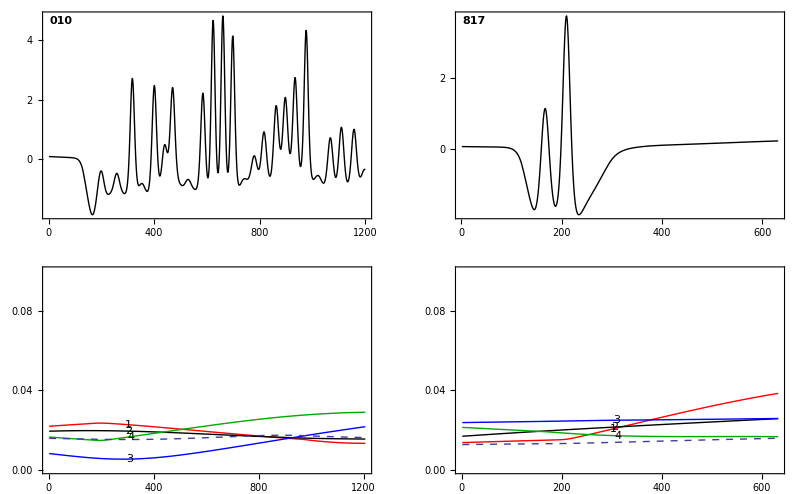

```mathematica
GraphicsGrid[{pedft,ppossq}ᵀ[[{2,5}]]ᵀ,ImageSize->Full]
```

```mathematica
Animate[Graphics3D[{Yellow,Sphere[#,.1]&/@pos[[i]],White,Table[Text[j,pos[[i,j]]],{j,16}],Gray, Sphere[posh[[i]],.05]}, PlotRange->{{-0.1,1.1},{-.1,1.1},{-.1,1.1}}],{i,1,Length[pos],1}]
```